# Equilibrium Torus

## References

Chakrabarti, S.K. 1985, ApJ, 288, 1
De Villiers, J.P., &  Hawley, J.F. 2003, ApJ, 589, 458

```mathematica
Clear[r,th,ut,l,lin,ut, omk, omega, omegain, lk, lin, l, p, n, cc,c,utin,lin, udt,k,al, omk,a,l,c,x,z,p,th, gtt, gtp, gpp, gutt, gutp, gupp]
```

### Parameters

```mathematica
(* physics *)
a=0.;
M=1;
KK=0.01; (* entropy constant *)
n=2-1.65; (* the power of lambda in DHK03. *)
rin=20; (* torus inner edge *)
Rmax=35; (* torus pressure maximum *)
gam=4/3;
hoverr=0.07; (* *new definition.* only used when checking half grid cells inside the disk *)
Δphi=π/2; (* only for checking the grid *)
β=100; (* only for checking the grid *)

(* grid *)
nx=256;
ny=64;
nz=32; (* only for checking the grid and printing data to "mytest" *)
Rin=0.92 Rm;
Rout=50;
R0=0.3;
hslope=0.13;
rhomin=10^-32;
theta[0]=0.;

SetDirectory["/Users/rpenna/Desktop"];
```

### Grid

```mathematica
startx1= Log[Rin-R0];
startx2=0;
dx1=Log[(Rout-R0)/(Rin-R0)]/nx;
dx2=1/ny;
startpos=1/2;

Array[rr,nx];
Array[dr,nx];
Array[theta,ny];
Array[dth, ny];

(* Kerr-Schild Coordinates *)
Do[x1[i]=startx1+(i-1+startpos)*dx1, {i,1,nx}];
Do[x2[i]=startx2+(i-1+startpos)*dx2, {i,1,ny}];
(* Boyer-Lindquist Coordinates *)
V1[i_]:=R0+Exp[x1[i]]
V2[i_]:= Pi/2 (hslope((x2[i]-0.5)/0.5)+ (1-theta[0]/(π/2)-hslope)*((x2[i]-0.5)/0.5)^7 +1)
Do[rr[i]=V1[i], {i,1,nx}];
Do[dr[i]=(rr[i]-R0)*dx1, {i,1,nx}];
Do[theta[i]=V2[i], {i,1,ny}];
Do[dth[j]= theta[j+1]-theta[j], {j, 1, ny-1}];

Do[Σ[i,j]=rr[i]^2+a^2 Cos[theta[j]]^2,{i,1,nx},{j,1,ny}]
Do[gdetbl[i,j]=Σ[i,j]Sin[theta[j]],{i,1,nx},{j,1,ny}]


Rmin= 1-Sqrt[1-a^2];
Rm= 1+Sqrt[1-a^2];

Print["Rmin(inner horizon)=",Rmin]
Print["rr[1]=",rr[1]]
Print[ "Rm(event horizon)=",Rm]
Print[]
If[rr[1]<Rmin,Print["Grid extends inside the inner horizon. WARNING."],Print["Grid begins outside the inner horizon. OK."]]


iBH=0;
Do[If[rr[i]<Rm,iBH=i,iBH=iBH],{i,1,nx}]
If[iBH<7,Print[iBH," grid cells inside the event horizon. WARNING."],If[iBH>8,Print[iBH," grid cells inside the event horizon. WARNING."],Print[iBH," grid cells inside the event horizon. OK."]]]

Z1=1+(1-a^2/M^2)^(1/3)((1+a/M)^(1/3)+(1-a/M)^(1/3));
Z2=(3 a^2/M^2+Z1^2)^(1/2);
rms=M(3+Z2-((3-Z1)(3+Z1+2Z2))^(1/2));
ims=0;
Do[If[rr[i]<rms,ims=i,ims=ims],{i,1,nx}]
If[(ims-iBH)>20,Print[(ims-iBH)," grid cells between the horizon and ISCO. OK."],Print[(ims-iBH)," grid cells between the horizon and ISCO. WARNING."]]


nyhr=0;
Do[If[Abs[theta[j]-π/2]<hoverr,nyhr=nyhr+1,Continue],{j,1,ny}]
Print[nyhr/2," grid cells per |h/r|"]


If[N[Δphi]>7 2π  hoverr 1/(√3),Print["Largest structures fit on ϕ-wedge (Δϕ=",N[Δphi]," > 7λ_m/r~",7 2π  hoverr 1/(√3),"). OK."],Print["Largest structures do NOT fit on ϕ-wedge (Δϕ=",N[Δphi]," < 7λ_m/r~",7 2π  hoverr 1/(√3),"). WARNING."]]
If[2 π hoverr 1/√β/dth[ny/2]>3,Print["Resolving MRI: λ_m/(rdθ)=",2 π hoverr 1/√β/dth[ny/2],". OK."],Print["Resolving MRI: λ_m/(rdθ)=",2 π hoverr 1/√β/dth[ny/2],". WARNING."]]
Print[]
Print["dr/rdθ at the ISCO=",dr[ims]/(rr[ims]dth[ny/2]), ". (2 is ideal.)"]
dph=Δphi/nz;
Print["rdϕ/dr at the equator=",(dph)/(dth[ny/2]) ,". (7 is ideal.)"]
```

Rmin(inner horizon)=0.

rr[1]=1.85049

Rm(event horizon)=2.

Grid begins outside the inner horizon. OK.

7 grid cells inside the event horizon. OK.

89 grid cells between the horizon and ISCO. OK.

11 grid cells per |h/r|

Largest structures do NOT fit on ϕ-wedge (Δϕ=1.5708 < 7λ_m/r~1.77752). WARNING.

Resolving MRI: λ_m/(rdθ)=6.89231. OK.

dr/rdθ at the ISCO=2.01907. (2 is ideal.)

rdϕ/dr at the equator=7.69231. (7 is ideal.)

### Computations

```mathematica
(* metric stuff *)
sig= r^2+a^2 Cos[th]^2;
del= r^2- 2 r M +a^2;
A=(r^2+a^2)^2- a^2 del Sin[th]^2;
gtt=-(1- 2 r/sig);
gtp=-(2 a r Sin[th]^2/sig);
gthth=sig;
gpp=Sin[th]^2 (a^2+r^2+2 a^2 M r Sin[th]^2/sig);
gab={{gtt, 0,0, gtp},{0,grr, 0, 0}, {0,0,gthth,0},{gtp, 0,0,gpp}};

gutt=-1-(4 r (a^2+r^2))/((a^2+(-2+r) r) (a^2+2 r^2+a^2 Cos[2 th]));
gutp=-(4 a r)/((a^2+(-2+r) r) (a^2+2 r^2+a^2 Cos[2 th]));
gupp=(2 ((-2+r) r+a^2 Cos[th]^2) Csc[th]^2)/((a^2+(-2+r) r) (a^2+2 r^2+a^2 Cos[2 th]));
```

```mathematica
r=Rmax;
th=Pi/2;
omk=1./(Rmax^1.5+a);
lk=(gutp-omk gutt)/(gupp-omk gutp);
s1=NSolve[Log[omk] ==(2/n) Log[c]+(1-2/n) Log[ lk] , c][[1]];
c=c /. %;

iin=0;
Do[If[V1[i]<rin,iin=i,iin=iin],{i,1,nx}]
imax=0;
Do[If[V1[i]<Rmax,imax=i,imax=imax],{i,1,nx}]

r=rin;
th=Pi/2;
Clear[gtt, gtp, gpp]
sig= r^2+a^2 Cos[th]^2;
bdel= r^2- 2 r M +a^2;
A=(r^2+a^2)^2- a^2 del Sin[th]^2;
gtt=-(1- 2 r/sig);
gtp= (-2 a r Sin[th]^2/sig);
gpp= Sin[th]^2 (a^2+r^2+2 a^2 M r Sin[th]^2/sig);
gutt=-1-(4 r (a^2+r^2))/((a^2+(-2+r) r) (a^2+2 r^2+a^2 Cos[2 th]));
gutp=-(4 a r)/((a^2+(-2+r) r) (a^2+2 r^2+a^2 Cos[2 th]));
gupp=(2 ((-2+r) r+a^2 Cos[th]^2) Csc[th]^2)/((a^2+(-2+r) r) (a^2+2 r^2+a^2 Cos[2 th]));

k=c^(2/n);
al=(n-2)/n;
```

```mathematica
al;
FindRoot[(gutp-lin gupp)/( gutt- lin gutp)==k lin^(al), {lin,4} ] ;
lin=lin /.%;
(gutp-lin gupp)/( gutt- lin gutp)-k lin^(al);
```

```mathematica
(* finding DHK03 lin, utin, f(lin) *)
utin=-Sqrt[ -1/(gutt - 2 lin gutp +lin^2 gupp)];
flin=Abs[1-k lin^(al+1)]^(1/(al+1));
```

```mathematica
Clear[r, th,f,q]
sig= r^2+a^2 Cos[th]^2;
del= r^2- 2 r M +a^2;
A=(r^2+a^2)^2- a^2 del Sin[th]^2;
gtt=-(1- 2 r/sig);
gtp=- (2 a r Sin[th]^2/sig);
gpp=Sin[th]^2 (a^2+r^2+2 a^2 M r Sin[th]^2/sig);
gutt=-1-(4 r (a^2+r^2))/((a^2+(-2+r) r) (a^2+2 r^2+a^2 Cos[2 th]));
gutp=-(4 a r)/((a^2+(-2+r) r) (a^2+2 r^2+a^2 Cos[2 th]));
gupp=(2 ((-2+r) r+a^2 Cos[th]^2) Csc[th]^2)/((a^2+(-2+r) r) (a^2+2 r^2+a^2 Cos[2 th]));

Print[a," ",lin];
```

0. 5.20068

```mathematica
(* setting up the grid *)
```

```mathematica
Array[lar,{nx,ny}];
Array[hh, {nx,ny}];
Array[f, {nx,ny}];
Array[udt,{nx,ny}];
Array[eps,{nx,ny}];
Array[rho, {nx,ny}];
Array[hr, {nx}];
Clear[r,th,q];
sig= r^2+a^2 Cos[th]^2;
del= r^2- 2 r M +a^2;
A=(r^2+a^2)^2- a^2 del Sin[th]^2;
gtt=-(1- 2 r/sig);
gtp=- (2 a r Sin[th]^2/sig);
gpp= Sin[th]^2 (a^2+r^2+2 a^2 M r Sin[th]^2/sig);

gutt=-1-(4 r (a^2+r^2))/((a^2+(-2+r) r) (a^2+2 r^2+a^2 Cos[2 th]));
gutp=-(4 a r)/((a^2+(-2+r) r) (a^2+2 r^2+a^2 Cos[2 th]));
gupp=(2 ((-2+r) r+a^2 Cos[th]^2) Csc[th]^2)/((a^2+(-2+r) r) (a^2+2 r^2+a^2 Cos[2 th]));
(* just put any value for dth[ny]...just for calculating h/r later. unimportant since rho~0 here. *)
dth[64]=.1;
```

```mathematica
(* starting from the inner edge on the equator, solving the grid *)
(* only for r > rin *)
lold=lin;

Do[

Do[
		
r=rr[i];
th=theta[j];
q=FindRoot[(l/c)^(-2/n)-((gutp- l gupp)/( l gutt -l^2 gutp))==0,{l,lold}];

lar[i,j]= l /. q;
l=l /. q ;
lold=lar[i,j];
			
     udt[i,j]=-Sqrt[- 1/(gutt - 2 l gutp +l^2 gupp)];
f[i,j]=Abs[1- k l^(al+1)]^(1/(al+1));
 hh[i,j]=utin flin/( udt[i,j]*f[i,j]);
eps[i,j]=1/gam (hh[i,j]-1);

rho[i,j]= (eps[i,j] (gam-1)/KK)^(1/(gam-1));

om[i,j]=(gutp- lar[i,j] gupp)/( gutt- lar[i,j] gutp);
If[Im[rho[i,j]]==0 && r>rin,rho[i,j]=rho[i,j], rho[i,j]=rhomin ],
{j,ny/2+1,ny}];
lold=lar[i,ny/2+1],
{i,iin,nx}]
```

```mathematica
lold=lin;
Do[
Do[
	
r=rr[i];
th=theta[j];

q=FindRoot[(l/c)^(-2/n)-((gutp- l gupp)/( l gutt -l^2 gutp))==0,{l,lold}];

lar[i,j]= l /. q;
l=l /. q ;
lold=lar[i,j];
			
     udt[i,j]=-Sqrt[- 1/(gutt - 2 l gutp +l^2 gupp)];
f[i,j]=Abs[1- k l^(al+1)]^(1/(al+1));
 hh[i,j]=utin flin/( udt[i,j]*f[i,j]);
eps[i,j]=1/gam (hh[i,j]-1);

rho[i,j]= (eps[i,j] (gam-1)/KK)^(1/(gam-1));

om[i,j]=(gutp- lar[i,j] gupp)/( gutt- lar[i,j] gutp);
If[Im[rho[i,j]]==0 && r>rin,rho[i,j]=rho[i,j], rho[i,j]=rhomin ],
{j,ny/2,1, -1}];
lold=lar[i,ny/2+1],
{i,iin,nx}]
```

```mathematica
Clear[R]
Do[
Do[
r=rr[i];
th=theta[j];
R[i,j]= r Sin[th];
If[r< rin|| Im[rho[i,j]]≠0 || rho[i,j]<0, rho[i,j]=rhomin ,rho[i,j]=rho[i,j] ];
If[r<rin|| Im[om[i,j]]≠0 || om[i,j]<0 , om[i,j]=0.,om[i,j]=om[i,j]],
{j, 1, ny}],
{i, 1,nx}]
```

## Appendix: Magnetic field setup

Vector potential:

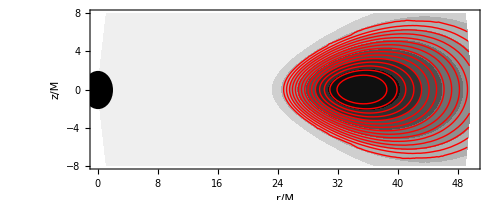

b^2:

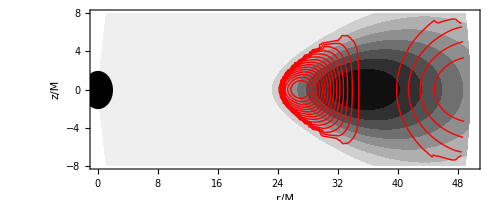

beta vs. radius:

-Graphics-

-Graphics-

```mathematica
(* Find rhomax *)
rhomax=0;
Do[If[rho[i,j]>rhomax,rhomax=rho[i,j],rhomax=rhomax],{i,iin,nx},{j,1,ny}]


(* Define internal energy *)
Do[uu[i,j]=rho[i,j]*eps[i,j],{i, 1,nx},{j,1,ny}];


(* DEFINE VECTOR POTENTIAL Subscript[A, ϕ]: *)
Do[uq[i,j]=rho[i,j]/rhomax-0.25,{i,1,nx},{j,1,ny}];
Do[If[uq[i,j]>0,Apot[i,j]=uq[i,j],Apot[i,j]=0.],{i, 1,nx},{j,1,ny}];

Atable=Flatten[Table[{rr[i]Sin[theta[j]],rr[i]Cos[theta[j]],Apot[i,j]},{j,1,ny},{i,1,nx}],1];


(* Magnetic field, B *)
top=1;
bot=ny-1;
Do[dApotdr[i,j]=(Apot[i+1,j]-Apot[i-1,j])/(rr[i+1]-rr[i-1]),{i,2,nx-1},{j,2,ny-1}]
Do[Br[i,j]=Apot[i,j]/(rr[i] Tan[theta[j]]),{i,2,nx-1},{j,2,ny-1}]
Do[Bθ[i,j]=-Apot[i,j]/rr[i]-dApotdr[i,j],{i,2,nx-1},{j,2,ny-1}]
Do[bsq[i,j]=Br[i,j]^2+rr[i]^2 Bθ[i,j]^2,{i,2,nx-1},{j,2,ny-1}]
Do[beta[i,j]=(gam-1)uu[i,j]/(0.5 bsq[i,j]+1*^-20),{i,2,nx-1},{j,2,ny-1}]


(* Normalize magnetic field *)
bsqavg=0;
uuavg=0;
Do[If[uq[i,j]>0,bsqavg=bsqavg+bsq[i,j]*gdetbl[i,j]*dr[i]*dth[j]],{i,2,nx-1},{j,2,ny-1}]
Do[If[uq[i,j]>0,uuavg=uuavg+uu[i,j]*gdetbl[i,j]*dr[i]*dth[j]],{i,2,nx-1},{j,2,ny-1}]
betanorm=(gam-1)uuavg/(0.5 bsqavg);
Do[beta[i,j]=beta[i,j]*100/betanorm,{i,2,nx-1},{j,2,ny-1}]


(* Tables and plots *)
rhotable=Flatten[Table[{rr[i]Sin[theta[j]],rr[i]Cos[theta[j]],-rho[i,j]},{i,1,nx},{j,1,ny}],1];
Bsqtable=Flatten[Table[{rr[i]Sin[theta[j]],rr[i]Cos[theta[j]],bsq[i,j]},{i,iin,nx-1,1},{j,top,bot,1}],1];
ymax=8;
rhor=2;
rmin=0;
Aphiplot=ListContourPlot[Atable,
AspectRatio->Automatic,
Contours->15,
PlotRange->{{rmin,50},{-ymax,ymax},Full},
ContourShading->False,
ContourStyle->Directive[Red,Thick],
ContourLabels->None,
FrameStyle->Directive[20],
FrameLabel->{"r/M","z/M"},
RegionFunction->Function[{x,y,z},Norm[x]<Rout &&Norm[y]<ymax&& Norm[x^2+y^2]>0.98^2 rhor]];

bsqplot=ListContourPlot[Bsqtable,
AspectRatio->Automatic,
Contours->15,
PlotRange->{{rmin,50},{-ymax,ymax},Full},
ContourShading->False,
ContourStyle->Directive[Red,Thick],
ContourLabels->None,
FrameStyle->Directive[20],
FrameLabel->{"r/M","z/M","b^2"},
RegionFunction->Function[{x,y,z},Norm[x]<Rout &&Norm[y]<ymax&& Norm[x^2+y^2]>0.98^2 rhor]];

rhoplot=ListContourPlot[rhotable,
AspectRatio->Automatic,
PlotRange->{{0,50},{-ymax,ymax}},
FrameStyle->Directive[20],
ContourLines->False,
ContourLabels->None,
ColorFunction->GrayLevel,
FrameLabel->{"r/M","z/M"},
RegionFunction->Function[{x,y,z},Norm[x]<Rout &&Norm[y]<ymax&& Norm[x^2+y^2]>0.98^2 rhor]];


blackhole=Graphics[Disk[{0,0},2]];
Print["Vector potential:"]
Show[{rhoplot,Aphiplot,blackhole}]
Print["b^2:"]
Show[{rhoplot,bsqplot,blackhole}]
Print["beta vs. radius:"]
ListPlot[Table[{rr[i],beta[i,32]},{i,200,250}],Joined->True,FrameLabel->{"r/M","β"},Frame->True,PlotRange->{0,50},FrameStyle->16,PlotStyle->Thick]
ListPlot[Table[{rr[i],beta[i,32]},{i,200,250}],Joined->True,FrameLabel->{"r/M","β"},Frame->True,PlotRange->{0,200},FrameStyle->16,PlotStyle->Thick]
```